```mathematica
NotebookEvaluate[NotebookOpen[StringJoin[NotebookDirectory[],"file-ops.nb"]]];
```

```mathematica
(*** PREDICTIONS ***)
Clear[predRfMonFPRTheor];

predRfMonFPRTheor[detFNR_, dInProp_, pDetNCH0_:0(* for this context *)] := 1 -(1 - detFNR + pDetNCH0)^(dInProp+1);
```

```mathematica
(*** ANALYSIS ***)
```

```mathematica
Clear[getRfFPRPointEstsWithMonH0ct, getRfFNRPointEstResidualsWithH0ct, getRfFprMSQPairsWithBins];

(* provides a list of triples: (monH0InfoCt, our RF mon FPR est, data RF mon FPR est) *) 
getRfFPRPointEstsWithMonH0ct[seshNums_, sampleCtPerSubset_, winSize_ ]:= tallyInfoInTriplesets[({#,predRfMonFPRTheor[predFNRfromData[#, detFilenames], winSize], predFPRfromData[#, monFilenames, winSize,(*mon num*)11]}&/@ sampleAcrossAllStatelessSubsets[seshNums, sampleCtPerSubset]), "h0count",monFilenames, winSize, 11];

(* KINDA USELESS: provides a list of triples: (monH1InfoCt, our mon FNR est, data mon FNR est) *) 
(*getFNRPointEstsWithDetH1ct[seshNums_, sampleCtPerSubset_, winSize_ ]:= tallyInfoInTriplesets[({#,predMonFNRTheor[predFPRfromData[#, detFilenames], winSize], predFNRfromData[#, monFilenames, winSize]}&/@ sampleAcrossAllSubsets[seshNums, sampleCtPerSubset]), "h1count",detFilenames, winSize];*)


(* provides a list of absolute residuals for above: (h1InfoCt, abs residual for our mon FNR est, abs residual for data mon FNR est) *) 
getRfFNRPointEstResidualsWithH0ct[seshNums_, sampleCtPerSubset_, winSize_] := With[{gtValue=predRfMonFPRTheor[0.1, winSize]},({#[[1]], Abs[#[[2]]-gtValue],Abs[#[[3]]-gtValue]  } & /@ getRfFPRPointEstsWithMonH0ct[seshNums, sampleCtPerSubset, winSize])];



(* privides a list of (bin start, bin elem count, mean squared error for our appr, mean squared error for data appr) ; bin end determined by bin size *) 
getRfFprMSQPairsWithBins[seshNums_, sampleCtPerSubset_, winSize_, binSize_]:= With[{h1CtTwoEstList= (*a list of triples (h0ct, our fpr est, data fpr est *) getRfFNRPointEstResidualsWithH0ct[seshNums, sampleCtPerSubset, winSize] },
(* convert h1cts into bin starts *) Flatten[#]&/@Transpose[{(Range[0,  Max@h1CtTwoEstList[[All,1]], binSize]),({Length@#, Mean@(#[[All,2]]^2), Mean@(#[[All,3]]^2)} &/@ binListsBy[h1CtTwoEstList, {First, 0, Max@h1CtTwoEstList[[All,1]]+binSize-1, binSize}])}]];
```

```mathematica
(*** PLOTS PRE CORRECTION-- WRONG ***) 

(* exact estimates plots *) 
(* win = 5 idk what's happening here  *) 

With[{data=getRfFPRPointEstsWithMonH0ct[{4,5,6,7},5, 5]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predRfMonFPRTheor[0.1, 5], Max@data[[All,1]]]]]
```

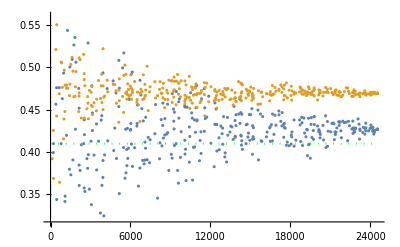

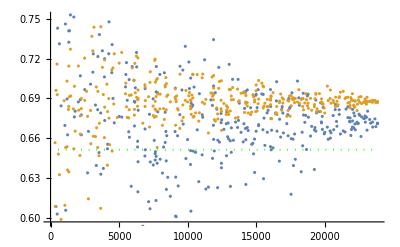

```mathematica
(* win = 10, ugh -- WRONG *) 
With[{data=getRfFPRPointEstsWithMonH0ct[{4,5,6,7},5, 10]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predRfMonFPRTheor[0.1, 10], Max@data[[All,1]]]]]
```

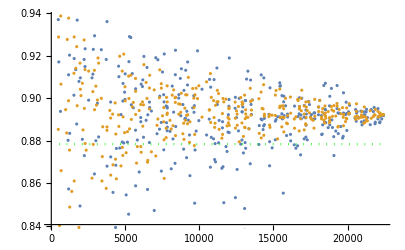

```mathematica
(* win of 20, very confused -- WRONG  *)
With[{data=getRfFPRPointEstsWithMonH0ct[{4,5,6,7},5, 20]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predRfMonFPRTheor[0.1, 20], Max@data[[All,1]]]]]
```

```mathematica
(* MSE BINNED, WEIRD *)
```

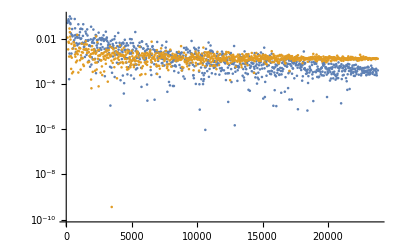

```mathematica
(* this one makes no sense at all; need bigger bins, too *) 
Clear[data];(data = getRfFprMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)40, (*win size *)10, (* bin width *)25];
ListLogPlot[{data[[All,{1,3}]], data[[All,{1,4}]]}, PlotRange->All])
```

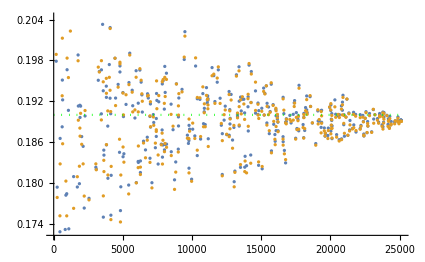
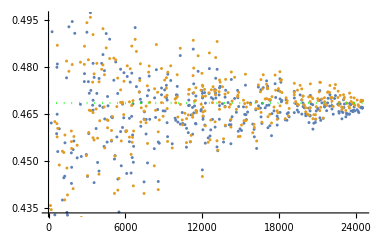
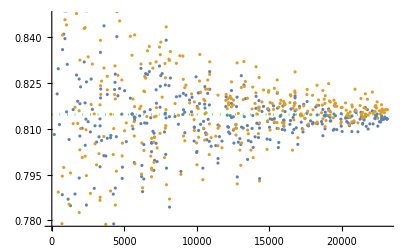
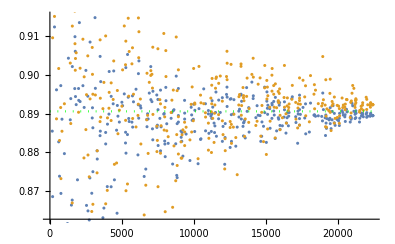
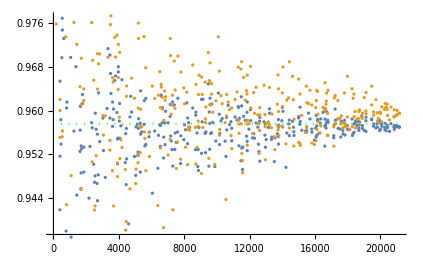
```mathematica
(** FIXED CONVERGENCE CHARTS **) 
With[{data=getRfFPRPointEstsWithMonH0ct[{4,5,6,7},5, #]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]}], chartHorLine[predRfMonFPRTheor[0.1, #], Max@data[[All,1]]]]] & /@ {1, 5, 10, 15, 20, 29} 
{-Graphics-,-Graphics-,for that $d$,-Graphics-,-Graphics-,-Graphics-}
```

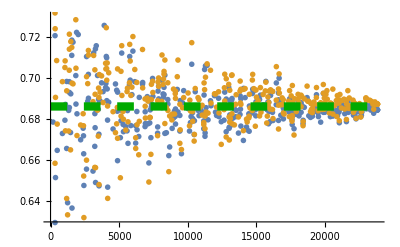

```mathematica
(* PRODUCTION READY EST CHART (no ci line) *)
plotRfFpr= With[{data=getRfFPRPointEstsWithMonH0ct[{4,5,6,7},5, 10]},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]},PlotRange->{0.63,0.73}, PlotMarkers->{"OpenMarkers", Large}], chartHorLine[predRfMonFPRTheor[0.1, 10], Max@data[[All,1]],0, Darker@Green, {AbsoluteThickness[6],AbsoluteDashing[12]}]]]
```

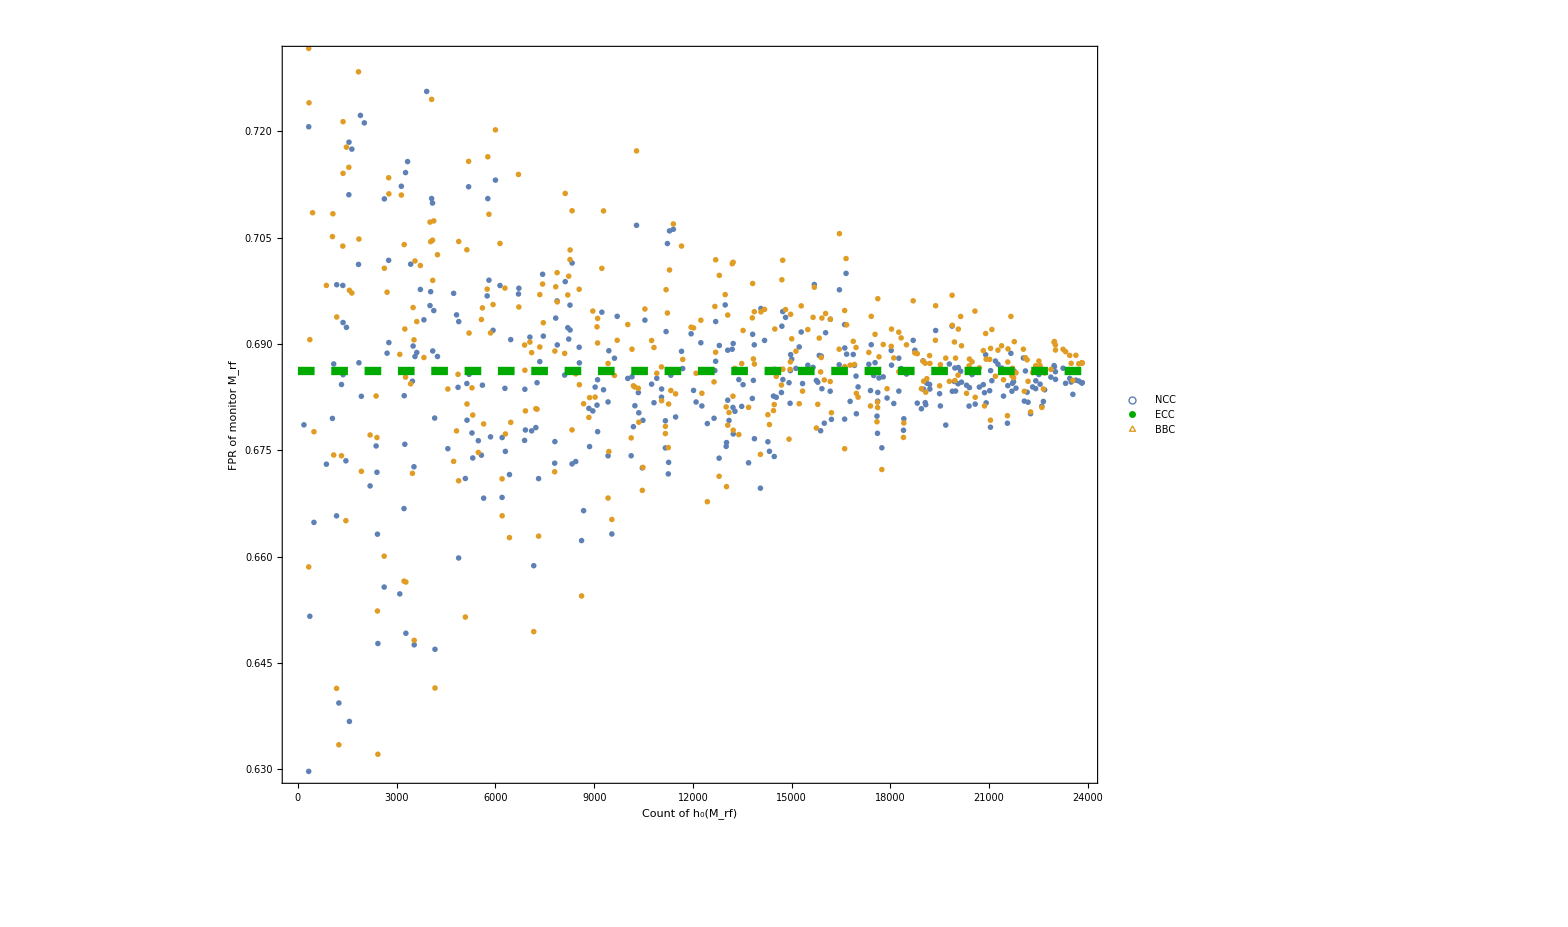

```mathematica
(* no CI line *)
plotRfFprLegended = Legended[Show[plotRfFpr, Frame->True, FrameLabel->{StringJoin["Count of ", ToString[ Style[StringJoin[ToString[Subscript[ "h", "0"],StandardForm], "(",ToString[Subscript[ "M", "rf"],StandardForm] ,")"], Italic], StandardForm] ],StringJoin["FPR of monitor ", ToString[Style[Subscript[ "M", "rf"],Italic], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->35}], Placed[PointLegend[Directive@@@{{ColorData[97,"ColorList"][[1]]},{AbsoluteDashing[6],AbsoluteThickness[4],Darker@Green} , {ColorData[97,"ColorList"][[2]]}},{"NCC","ECC", "BBC"},
LegendMarkerSize->20,LegendMarkers->{Style[○,Bold,FontSize->28] , Graphics[{Line[{{-10,0},{10,0}}]}],Style[△,Bold,FontSize->28] (*Graphics[{Thick,SSSTriangle[1,1,1]}]*)}],{0.9,0.2}]]
```

```mathematica
rfDataForNow = getRfFPRPointEstsWithMonH0ct[{4,5,6,7},(*samples per subset*)5, (*winsize*)10];
```

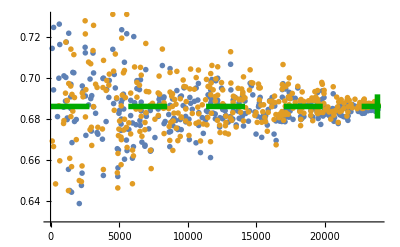

```mathematica
(* PRODUCTION READY EST CHART (with ci line) *)
plotRfFprWithCi= With[{data=rfDataForNow},Show[ListPlot[{data[[All,{1,2}]], data[[All,{1,3}]]},PlotRange->{0.63,0.73}, PlotMarkers->{Magnify[openMarkers[[1]], 4], Magnify[openMarkers[[2]],4]}], chartHorLine[predRfMonFPRTheor[0.1, (*winsize*)10], Max@data[[All,1]],0, Darker@Green, {Thickness[0.01],AbsoluteDashing[28]}],ListPlot[{{Max@data[[All,1]],interWald[Max@data[[All,1]]*predRfMonFPRTheor[0.1, (*winsize*)10], Max@data[[All,1]], 0.95] }}, PlotStyle->{Darker@Green,Thickness[0.01]}]]]
```

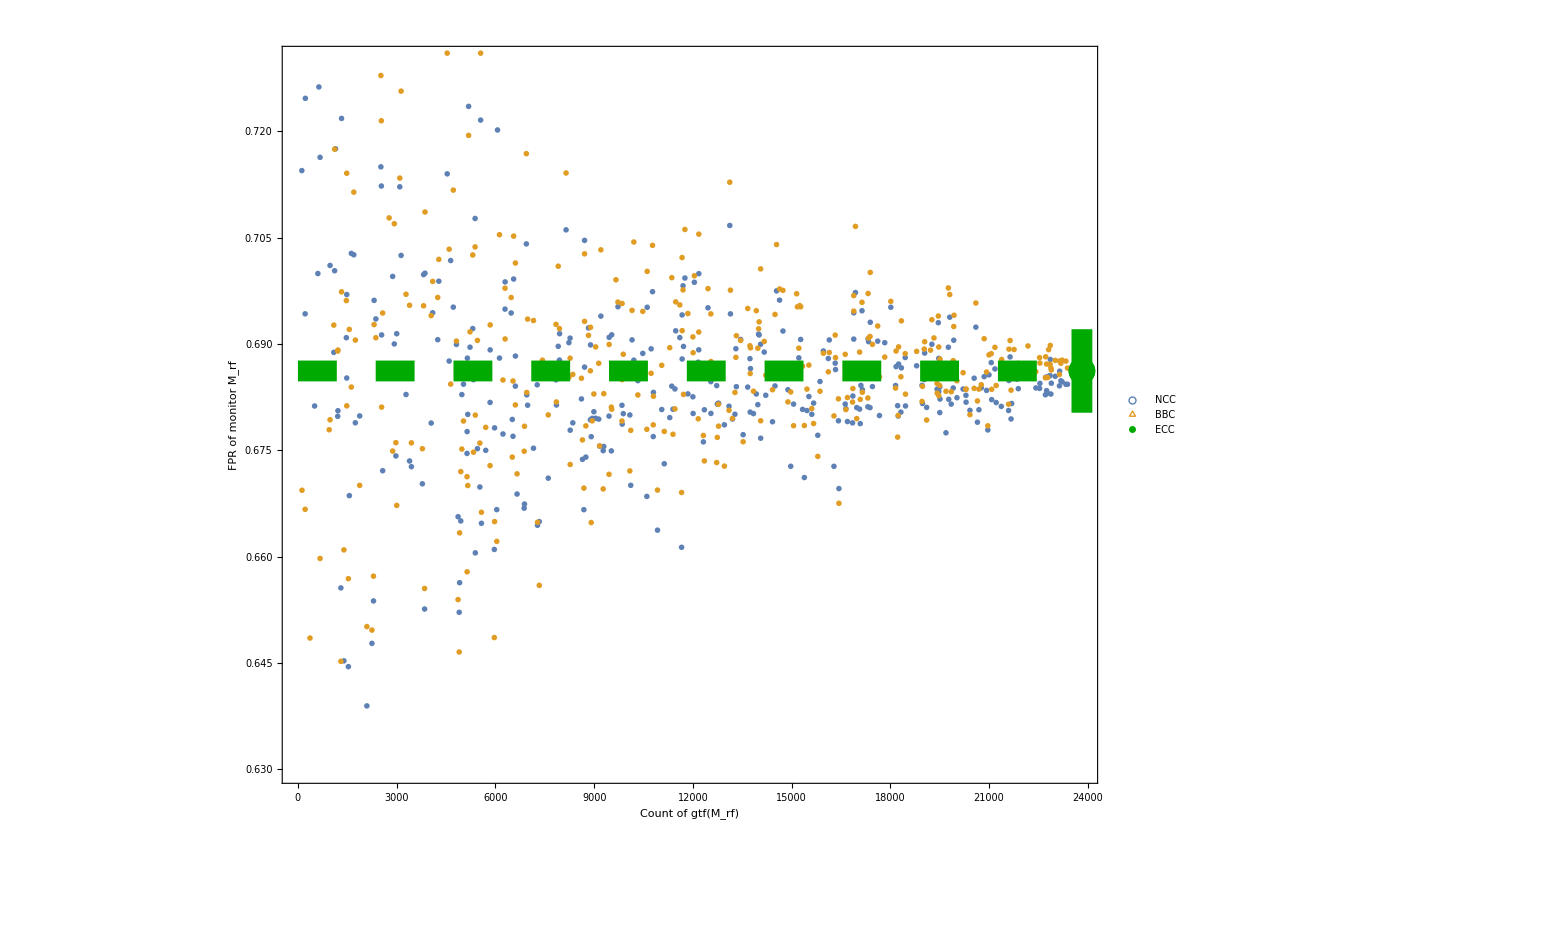

```mathematica
(* with CI line and legend *)
plotRfFprLegended = Legended[Show[plotRfFprWithCi, Frame->True, FrameLabel->{StringJoin["Count of gtf", ToString[ Style[StringJoin[ "(",ToString[Subscript[ "M", "rf"],StandardForm] ,")"], Italic], StandardForm] ],StringJoin["FPR of monitor ", ToString[Style[Subscript[ "M", "rf"],Italic], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->45}], Placed[PointLegend[Directive@@@{{ColorData[97,"ColorList"][[1]]},  {ColorData[97,"ColorList"][[2]]},{AbsoluteDashing[10],AbsoluteThickness[6],Darker@Green}},{"NCC","BBC","ECC" },
LegendMarkerSize->50,LegendMarkers->{Style[○,Bold,FontSize->55] ,Style[△,Bold,FontSize->60], Graphics[{Line[{{-10,0},{10,0}}]}](*Graphics[{Thick,SSSTriangle[1,1,1]}]*)}],{0.9,0.2}]]
```

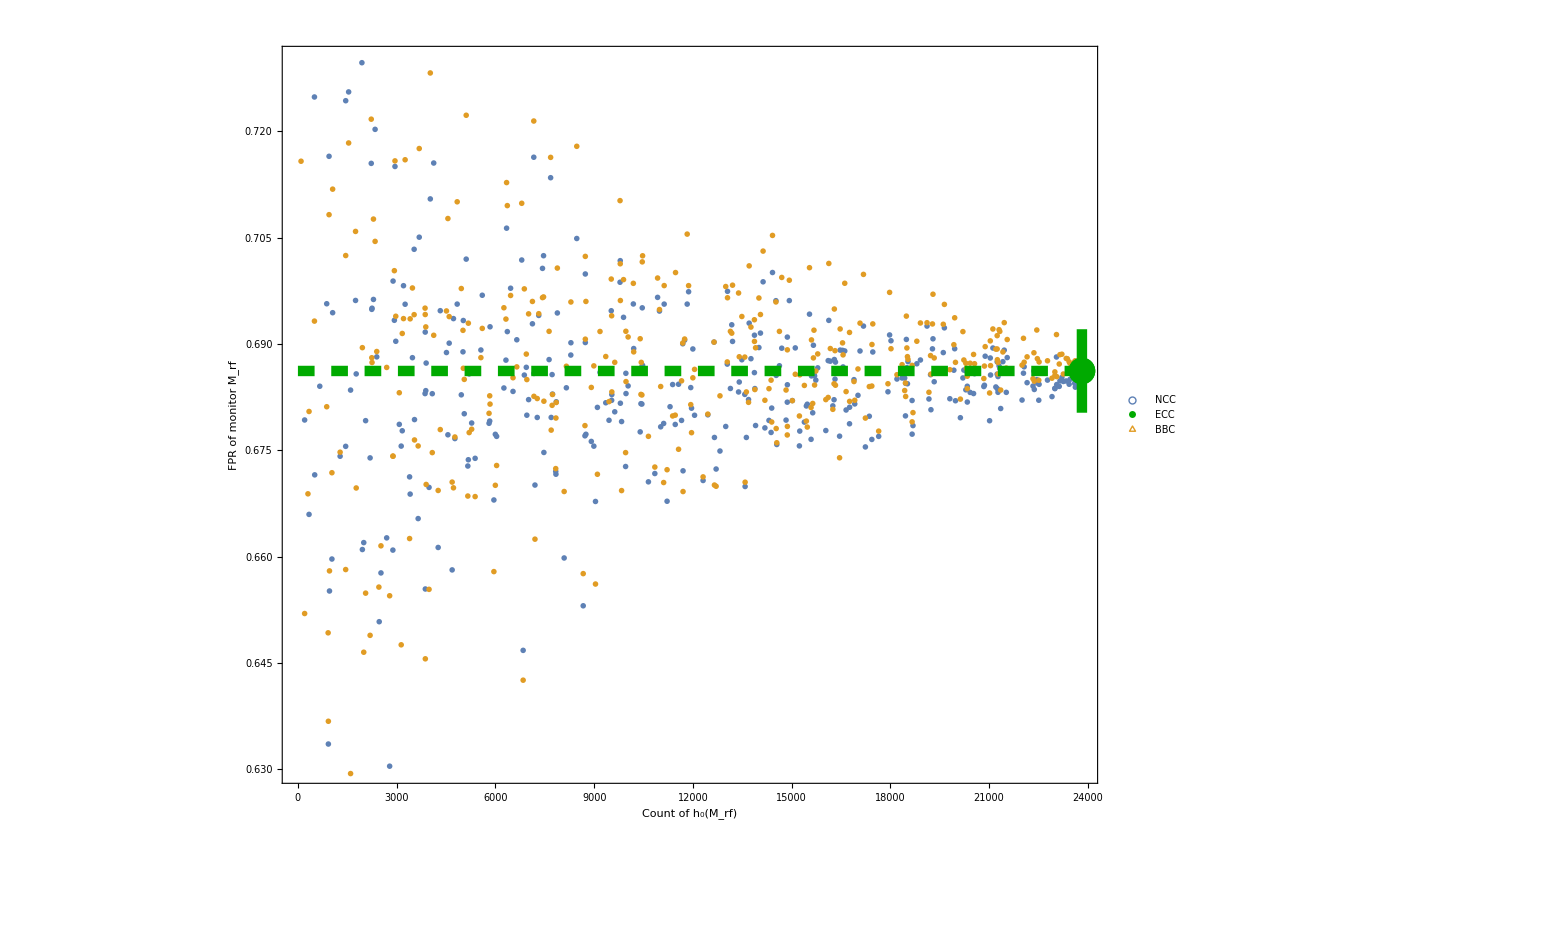

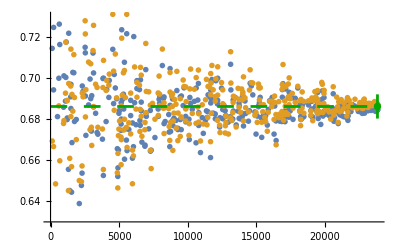

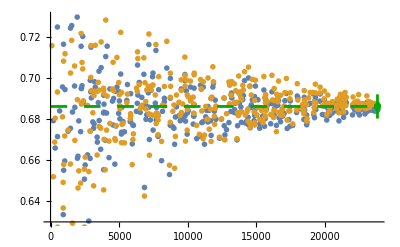

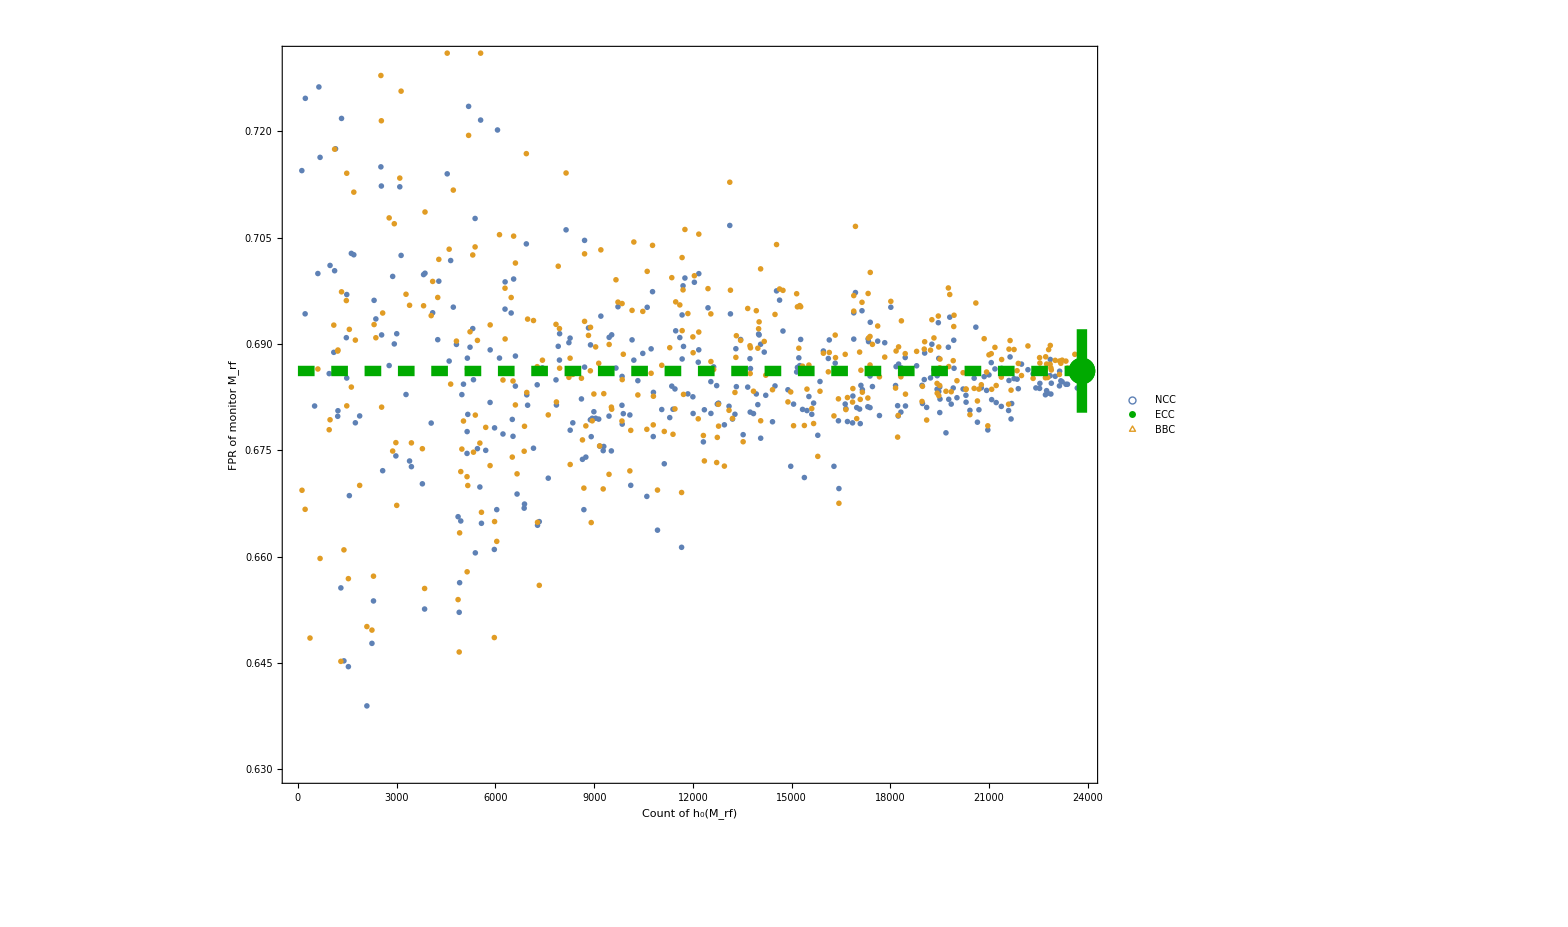

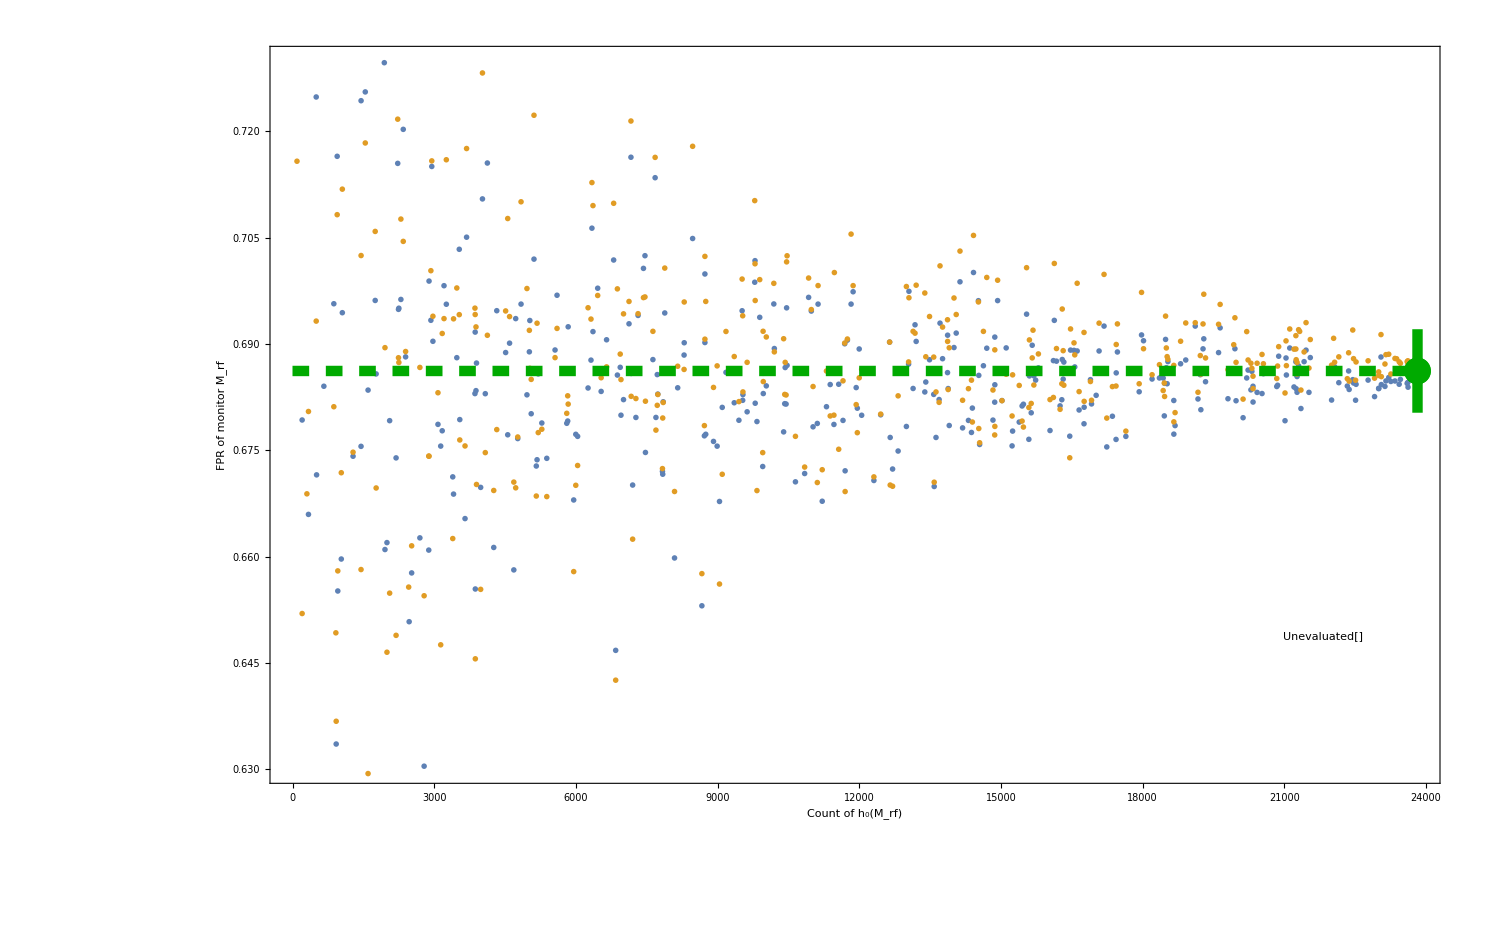

```mathematica
(* NOW MSE *) 

(* bins too small! *) 
(data = getRfFprMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)40, (*win size *) #, (* bin width *)150];
ListLogPlot[{data[[All,{1,3}]], data[[All,{1,4}]]}, PlotRange->All])&/@ Range[10,10]
```

```mathematica
data
```

{{0,3,0.0173813,0.0176151},{150,17,0.00444687,0.00700641},{300,17,0.00486905,0.00702227},{450,28,0.0032834,0.00461906},{600,24,0.00183857,0.00228872},{750,19,0.00177343,0.00214039},{900,18,0.000929241,0.00194973},{1050,8,0.000423822,0.00114171},{1200,13,0.00118192,0.0018089},{1350,19,0.0014865,0.00160534},{1500,22,0.00107045,0.00219132},{1650,17,0.00151737,0.0026008},{1800,20,0.000860545,0.00101091},{1950,23,0.000447746,0.000938793},{2100,20,0.000332719,0.000772963},{2250,22,0.000630723,0.00106573},{2400,20,0.000528846,0.000923399},{2550,19,0.000687276,0.000899638},{2700,15,0.000614551,0.00109194},{2850,16,0.000236084,0.000527141},{3000,18,0.00034882,0.000339053},{3150,19,0.000312487,0.000580436},{3300,20,0.000150075,0.000239905},{3450,15,0.000539886,0.00039461},{3600,17,0.000277192,0.00026894},{3750,21,0.000528113,0.000687688},{3900,13,0.000342389,0.000595715},{4050,22,0.000246688,0.000494802},{4200,21,0.000373314,0.000372151},{4350,11,0.000329929,0.000425961},{4500,18,0.0002625,0.000304523},{4650,13,0.00019192,0.000438341},{4800,15,0.000192879,0.000336234},{4950,14,0.000311011,0.000474755},{5100,25,0.000236381,0.000305997},{5250,19,0.000181176,0.00029565},{5400,15,0.000446006,0.000475148},{5550,19,0.000213475,0.000339495},{5700,24,0.000210284,0.000405057},{5850,18,0.000382005,0.000359205},{6000,14,0.000228928,0.000216909},{6150,13,0.000238696,0.000348015},{6300,19,0.000246125,0.000333411},{6450,21,0.000149383,0.000243003},{6600,20,0.000265681,0.00025981},{6750,22,0.000238778,0.000247598},{6900,20,0.000148739,0.000153361},{7050,19,0.000357861,0.000275377},{7200,11,0.000178291,0.000402911},{7350,20,0.0000820293,0.000110718},{7500,21,0.000182143,0.000222316},{7650,23,0.000116837,0.000163268},{7800,23,0.0000889071,0.00017098},{7950,21,0.000118701,0.000179862},{8100,18,0.000139644,0.000129996},{8250,18,0.0000719434,0.0000956734},{8400,10,0.0000846243,0.000215796},{8550,26,0.000106635,0.000106235},{8700,21,0.000123454,0.000181213},{8850,17,0.000112984,0.000147083},{9000,18,0.00012603,0.000117749},{9150,26,0.00015107,0.00019774},{9300,14,0.0000791308,0.000122821},{9450,14,0.00014345,0.000224454},{9600,14,0.0000787757,0.000099847},{9750,19,0.0000891163,0.000112192},{9900,13,0.000166404,0.000223426},{10050,11,0.000119828,0.000110723},{10200,22,0.0000988982,0.000114361},{10350,14,0.0000550395,0.000069243},{10500,21,0.0000848587,0.00018119},{10650,13,0.0000942593,0.0000485652},{10800,19,0.0000667535,0.000135038},{10950,16,0.0000797711,0.000103662},{11100,21,0.0000723589,0.000116738},{11250,16,0.000117266,0.000157575},{11400,23,0.0000316845,0.0000698951},{11550,17,0.0000920649,0.00011824},{11700,20,0.0000774339,0.000111014},{11850,16,0.0000996532,0.000151902},{12000,23,0.0000781247,0.00010284},{12150,17,0.0000501541,0.0000330681},{12300,11,0.0000647532,0.0000853742},{12450,20,0.0000513836,0.000068109},{12600,22,0.0000581972,0.0000832778},{12750,12,0.0000891176,0.0000963719},{12900,23,0.0000674072,0.000112365},{13050,21,0.0000530413,0.0000690102},{13200,22,0.0000332259,0.0000909305},{13350,16,0.0000992797,0.0001333},{13500,22,0.0000499934,0.0000664365},{13650,19,0.0000676167,0.0000677358},{13800,17,0.0000660894,0.0000521361},{13950,20,0.0000532543,0.0000520865},{14100,24,0.0000466954,0.000066615},{14250,11,0.0000348067,0.0000494627},{14400,18,0.0000594558,0.0000448491},{14550,17,0.0000364489,0.0000545416},{14700,21,0.000035091,0.0000869558},{14850,14,0.0000917858,0.0000849926},{15000,22,0.0000381897,0.0000439232},{15150,18,0.0000320569,0.0000839954},{15300,18,0.0000344719,0.0000299584},{15450,22,0.0000271883,0.0000399722},{15600,12,0.0000484623,0.0000723423},{15750,23,0.0000319071,0.0000482374},{15900,13,0.0000229994,0.0000231131},{16050,17,0.0000390934,0.0000500987},{16200,17,0.0000431074,0.0000628413},{16350,16,0.0000217105,0.0000353639},{16500,20,0.0000181864,0.0000259185},{16650,14,0.0000327187,0.0000463049},{16800,20,0.0000313362,0.0000551098},{16950,20,0.0000233038,0.0000213425},{17100,29,0.0000249943,0.0000290461},{17250,11,0.0000305157,0.0000322627},{17400,21,0.00001955,0.0000386936},{17550,15,0.000021211,0.0000370969},{17700,18,0.0000265677,0.0000574035},{17850,14,0.000023699,0.0000298239},{18000,16,0.0000218823,0.0000341669},{18150,27,0.000025359,0.0000286917},{18300,20,0.0000364218,0.0000295569},{18450,17,0.0000272926,0.0000216569},{18600,18,0.0000194655,0.0000213872},{18750,18,9.30486×10^-6,0.0000128231},{18900,17,0.000013499,0.0000195501},{19050,18,7.30421×10^-6,0.0000280081},{19200,23,0.0000236168,0.000035873},{19350,22,0.0000210966,0.0000261465},{19500,19,0.0000171342,0.0000208079},{19650,31,0.0000152268,0.000022016},{19800,18,0.0000146911,0.000028173},{19950,16,0.0000136142,0.000015096},{20100,15,0.0000131614,0.0000134757},{20250,22,0.00001349,0.000019643},{20400,12,0.0000175602,0.0000216817},{20550,18,0.0000135543,0.0000121224},{20700,17,9.15078×10^-6,0.00002112},{20850,22,9.28992×10^-6,0.0000185033},{21000,19,7.68967×10^-6,0.0000115907},{21150,17,0.0000119362,0.0000107728},{21300,17,0.0000178762,0.0000270651},{21450,20,0.0000124838,0.0000160877},{21600,24,0.0000127664,0.0000140055},{21750,17,6.59964×10^-6,7.91049×10^-6},{21900,19,6.90842×10^-6,0.0000194868},{22050,10,3.56954×10^-6,8.77878×10^-6},{22200,16,7.53557×10^-6,6.7495×10^-6},{22350,23,8.45208×10^-6,7.68199×10^-6},{22500,16,4.7139×10^-6,5.6903×10^-6},{22650,12,5.50371×10^-6,3.6353×10^-6},{22800,18,4.26078×10^-6,6.24194×10^-6},{22950,16,6.27335×10^-6,3.67369×10^-6},{23100,13,4.04569×10^-6,3.75963×10^-6},{23250,15,5.75101×10^-6,2.41476×10^-6},{23400,32,2.88603×10^-6,2.83538×10^-6},{23550,17,2.23894×10^-6,2.34336×10^-6},{23700,42,2.70632×10^-6,1.30601×10^-6}}

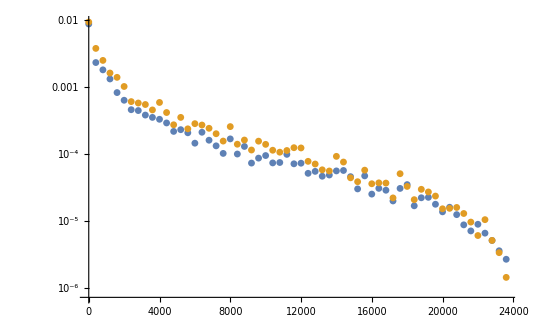

```mathematica
(data = getRfFprMSQPairsWithBins[ (* sessions *) {4,5,6,7},(*samples per subset size*)40, (*win size *) #, (* bin width *)400];
ListLogPlot[{data[[All,{1,3}]], data[[All,{1,4}]]}, PlotRange->All])&/@ Range[10,10]
```

```mathematica
data
```

```mathematica
mseRfdata= {{0,39,0.008753846063883951,0.009364130868615232},{400,43,0.002327274909250556,0.003786250647802682},{800,49,0.0018102315750221408,0.0025044283445789742},{1200,48,0.0013232966854286648,0.0016233764352973608},{1600,53,0.0008286104012448295,0.0013990184748609985},{2000,49,0.000636400610136973,0.001021699538341888},{2400,49,0.0004598834766204994,0.0006073842638642064},{2800,42,0.00044643159226292805,0.0005787157232414234},{3200,51,0.0003823659224167602,0.0005496409905057145},{3600,58,0.00035303471207587543,0.00045612877513680124},{4000,40,0.00033070940383937643,0.0005899910107008688},{4400,58,0.0002915924575237467,0.00041727653703346664},{4800,46,0.000218038282491525,0.0002736945155611596},{5200,47,0.00023137501087496957,0.00035296655448824446},{5600,45,0.00020798033813996446,0.00023814800189202203},{6000,60,0.00014539473507203414,0.00028442503550484677},{6400,36,0.00021179527179475576,0.0002714024345678539},{6800,51,0.00016101680389904221,0.00024271709491385503},{7200,38,0.0001327039152203665,0.00020125753425706162},{7600,59,0.0001023142760984767,0.00015633966952831774},{8000,49,0.00016854932695272964,0.0002571014489224543},{8400,54,0.00010017880036309966,0.0001403612019730609},{8800,43,0.0001300087452955154,0.00016203718493481133},{9200,42,0.00007336047055548691,0.00011497683922188153},{9600,47,0.00008699110782089908,0.0001558677770603709},{10000,47,0.00009504322457307208,0.00013966277560495275},{10400,58,0.00007380197600094737,0.00011408920660112812},{10800,50,0.00007482319446145787,0.00010669451812461147},{11200,49,0.00009905905834334047,0.00011301978240244829},{11600,48,0.00007155925895277674,0.00012449271462340993},{12000,49,0.00007306117476867106,0.00012347408499420535},{12400,45,0.000051582207120326154,0.00007789011068375261},{12800,52,0.00005518841966850562,0.00007106254062743468},{13200,42,0.00004669488301410268,0.000058187368247801654},{13600,59,0.00004867910173492783,0.00005589825087515436},{14000,55,0.00005605261722232227,0.00009243126222032096},{14400,42,0.00005686471758550254,0.00007603766682848013},{14800,55,0.00004599474287918309,0.00004420532780797283},{15200,40,0.000030182592213164602,0.00003865805750892839},{15600,44,0.00004726447274130192,0.000057502425982886124},{16000,47,0.000025241229117418147,0.000036032384434042424},{16400,41,0.00003077639351407714,0.00003717168419357862},{16800,62,0.000028836508850778292,0.00003686848717621848},{17200,56,0.00001994791520319732,0.000022145221994296557},{17600,44,0.00003069838984290998,0.00005089652128555963},{18000,45,0.00003498713862905976,0.00003286097392552741},{18400,47,0.000016881626015467054,0.000020847133586284943},{18800,59,0.000022244729225514516,0.00002976084987390388},{19200,45,0.000022591566849391056,0.000027185170015194626},{19600,49,0.00001780408426171681,0.00002359319081515364},{20000,37,0.000013720670578660453,0.000015232448539935677},{20400,60,0.00001605829419154737,0.0000154795821902473},{20800,52,0.000012462193061590095,0.000015955659916553164},{21200,49,8.767768725748333*^-6,0.000012957405613932393},{21600,48,7.117756138044823*^-6,9.64410305878872*^-6},{22000,47,8.944155663632217*^-6,6.074905052261932*^-6},{22400,45,6.591182778503149*^-6,0.000010483089886661216},{22800,56,5.1280809608469385*^-6,5.133801582651264*^-6},{23200,45,3.597002495132978*^-6,3.3711140903762794*^-6},{23600,55,2.685407281164483*^-6,1.4405526715560627*^-6}};
```

```mathematica
rmseRfdata = mseRfdata; rmseRfdata[[All,{3,4}]]  = Sqrt@rmseRfdata[[All,{3,4}]] ;
```

```mathematica
(* PRODUCTION READY MSE PLOT *)
```

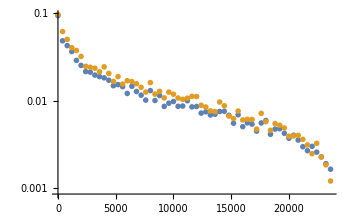

```mathematica
rmseRfplot = ListLogPlot[{rmseRfdata[[All,{1,3}]], rmseRfdata[[All,{1,4}]]}, PlotRange->All, PlotMarkers->{Magnify[openMarkers[[1]], 4], Magnify[openMarkers[[2]],4]}]
```

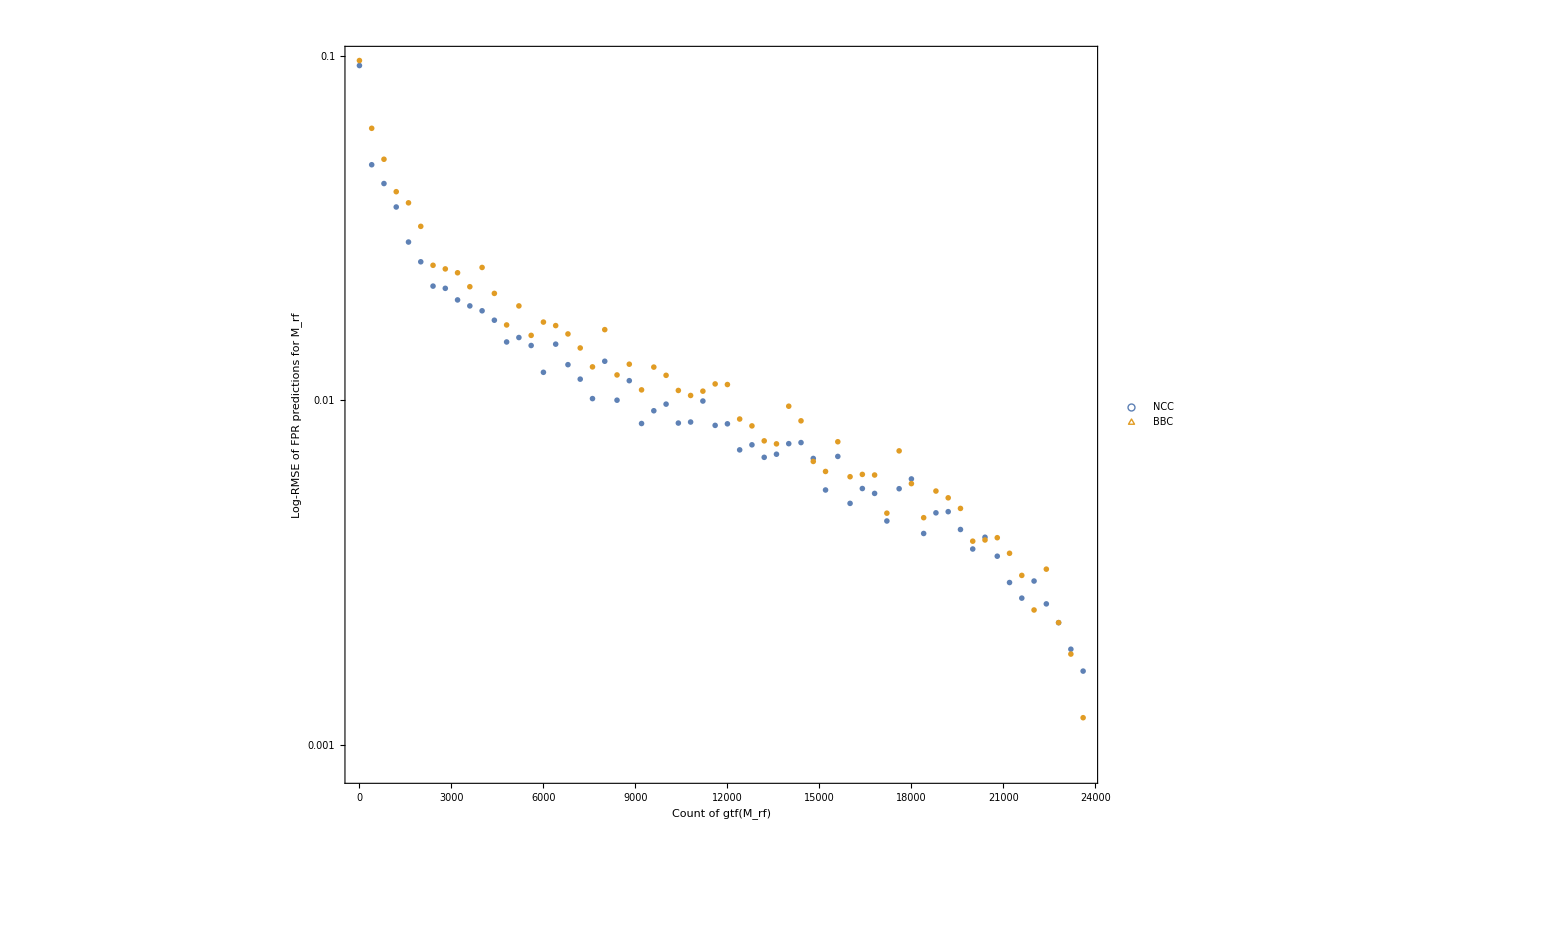

```mathematica
mseRfplotLegended = Legended[Show[rmseRfplot, Frame->True, FrameLabel->{StringJoin["Count of gtf", ToString[ Style[StringJoin["(",ToString[Subscript[ "M", "rf"],StandardForm] ,")"], Italic], StandardForm] ], StringJoin["Log-RMSE of FPR predictions for ", ToString[Subscript[ "M", "rf"], StandardForm]]}, ImageSize->1500, BaseStyle-> {FontSize->35}],Placed[PointLegend[Directive@@@{{ColorData[97,"ColorList"][[1]]} , {ColorData[97,"ColorList"][[2]]}},{"NCC", "BBC"},
LegendMarkerSize->50,LegendMarkers->{Style[○,Bold,FontSize->55] , Style[△,Bold,FontSize->60] (*Graphics[{Thick,SSSTriangle[1,1,1]}]*)}],{0.1,0.15}]]
```